Run the code to get a list of dictionary words that start with “z” and have four letters. Get words that have other patterns of letters (e.g. start with “a”, then have four letters):

l

Get a list of all dictionary words in English:

DictionaryLookup[]

{"a","Aachen","aah","Aaliyah","aardvark","aardvarks","Aaron","abaci","aback","abacus","abacuses","abaft","abalone","abalones","abandon","abandoned",92486,"Zululand","Zulus","Zuni","Zunis","Zurich","Zürich","zwieback","Zwingli","Zworykin","zydeco","zygote","zygotes","zygotic","zymurgy","Zyrtec","Zyuganov"}
 |  |  |  |

Get a list of words that match the pattern of starting with “z” and then having 3 more letters:

DictionaryLookup["z"~~_~~_~~_]

{"zany","zaps","zeal","zebu","zeds","zero","zest","zeta","zinc","zine","zing","zips","zits","zone","zoom","zoos"}

l

## -Graphics- -Graphics- -Graphics-

```mathematica
DictionaryLookup["z"~~_~~_~~_]
```

Find the five words that are “nearest” to “elephant”. Try out different words and see which other words are “nearest” (e.g. try your name):
Note: upper and lower case are considered different.

l

This finds 5 words nearest to “elephant”, based on changing the fewest letters:

Nearest[DictionaryLookup[],"elephant",5]

{"elephant","elephants","elegant","celebrant","eggplant"}

l

## -Graphics- -Graphics- -Graphics-

```mathematica
Nearest[DictionaryLookup[],"elephant",5]
```

Find all the words that differ from “fish” by one letter. Try out different words to find words that differ from them by one letter (e.g. try your name):
Note: longer words may have no nearby other words.

l

This finds all the words in the dictionary that differ from “fish” by at most 1 letter:

Nearest[DictionaryLookup[],"fish",{All,1}]

{"fish","dish","fishy","fist","Gish","wish"}

Use Restpaclet:ref/Rest to keep the “rest” of the list, dropping the original word:

Rest[Nearest[DictionaryLookup[],"fish",{All,1}]]

{"dish","fishy","fist","Gish","wish"}

l

## -Graphics- -Graphics- -Graphics-

```mathematica
Rest[Nearest[DictionaryLookup[],"fish",{All,1}]]
```

Make a network. Try making networks using different numbers than 2, 1, and 10:

l

We’re going to want to create networks of words. Let’s start by creating a network of numbers.

This defines a particular way to connect numbers from 0 to 9:

Table[n→Mod[2n+1,10],{n,0,9}]

{0→1,1→3,2→5,3→7,4→9,5→1,6→3,7→5,8→7,9→9}

Graphpaclet:ref/Graph draws a network or “graph”; VertexLabels->“Name” says to label vertices with their names:

Graph[Table[n→Mod[2n+1,10],{n,0,9}],VertexLabels→"Name"]

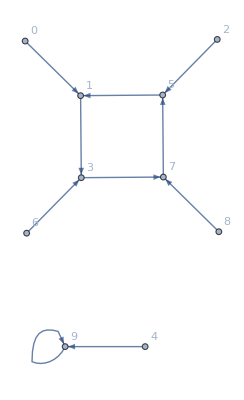

l

## -Graphics- -Graphics- -Graphics-

```mathematica
Graph[Table[n->Mod[2n+1,10],{n,0,9}],VertexLabels->"Name"]
```

Make a network of words that differ by one letter. Try making networks for different classes of words (e.g. words beginning with “w” instead of “q”):
Note: this will take a long time if your class of words is big.

l

This creates a list of words that are going to be in the network, here consisting of “q” followed by 3 letters:

words=DictionaryLookup["q"~~_~~_~~_]

{"quad","quay","quid","quin","quip","quit","quiz"}

We’re naming this list words.

Now we construct a function that finds nearest words:

nf=Nearest[words]

NearestFunction[…]

We can apply this function to any word in the list, saying we want all words that differ by at most 1 letter:

nf["quad",{All,1}]

{"quad","quay","quid"}

Use Restpaclet:ref/Rest to keep only the “rest” of the list, dropping the first element (which is here the original word):

Rest[nf["quad",{All,1}]]

{"quay","quid"}

To find the whole network, we need to apply this to every word in the list:

#->Rest[nf[#,{All,1}]]&/@words

{"quad"→{"quay","quid"},"quay"→{"quad"},"quid"→{"quad","quin","quip","quit","quiz"},"quin"→{"quid","quip","quit","quiz"},"quip"→{"quid","quin","quit","quiz"},"quit"→{"quid","quin","quip","quiz"},"quiz"→{"quid","quin","quip","quit"}}

The #paclet:ref/Slot and &paclet:ref/Function set up a pure function, which is then mapped over the original list of words.

To form the actual network, we need to “thread” these connections. Threadpaclet:ref/Thread turns a connection to a list into a list of connections—for example:

Thread["one"→{"two","three"}]

{"one"→"two","one"→"three"}

Thread the nearest connections:

Thread[#->Rest[nf[#,{All,1}]]]&/@words

{{"quad"→"quay","quad"→"quid"},{"quay"→"quad"},{"quid"→"quad","quid"→"quin","quid"→"quip","quid"→"quit","quid"→"quiz"},{"quin"→"quid","quin"→"quip","quin"→"quit","quin"→"quiz"},{"quip"→"quid","quip"→"quin","quip"→"quit","quip"→"quiz"},{"quit"→"quid","quit"→"quin","quit"→"quip","quit"→"quiz"},{"quiz"→"quid","quiz"→"quin","quiz"→"quip","quiz"→"quit"}}

Then flatten out all the sublists:

Flatten[Thread[#->Rest[nf[#,{All,1}]]]&/@words]

{"quad"→"quay","quad"→"quid","quay"→"quad","quid"→"quad","quid"→"quin","quid"→"quip","quid"→"quit","quid"→"quiz","quin"→"quid","quin"→"quip","quin"→"quit","quin"→"quiz","quip"→"quid","quip"→"quin","quip"→"quit","quip"→"quiz","quit"→"quid","quit"→"quin","quit"→"quip","quit"→"quiz","quiz"→"quid","quiz"→"quin","quiz"→"quip","quiz"→"quit"}

Now we can turn this into a graph, or network:

Graph[Flatten[Thread[#->Rest[nf[#,{All,1}]]]&/@words],VertexLabels→"Name"]

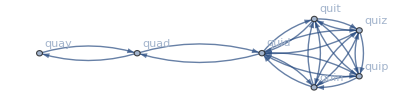

l

## -Graphics- -Graphics- -Graphics-

```mathematica
words=DictionaryLookup["q"~~_~~_~~_];
nf=Nearest[words];Graph[Flatten[Thread[#->Rest[nf[#,{All,1}]]]&/@words],VertexLabels->"Name"]
```

Run the first expression to set up a network of words with four letters. Then try some different words with four letters in the second expression (e.g. “pigs” or “nose”) to find word ladders between them:
Note: the words need to be in the dictionary.

l

This creates a network (named g) of nearest words for all 4-letter dictionary words (note that there’s a semicolon at the end to avoid printing the very big result):

words=DictionaryLookup[_~~_~~_~~_];
nf=Nearest[words];g=Graph[Flatten[Thread[#->Rest[nf[#,{All,1}]]]&/@words]];

This finds the shortest path on the network from “fish” to “fowl”—a word ladder:

FindShortestPath[g,"fish","fowl"]

{"fish","dish","dosh","bosh","boss","bows","bowl","fowl"}

l

## -Graphics- -Graphics- -Graphics-

```mathematica
words=DictionaryLookup[_~~_~~_~~_];
nf=Nearest[words];g=Graph[Flatten[Thread[#->Rest[nf[#,{All,1}]]]&/@words]];
```

Run this after you’ve run the previous expression:

```mathematica
FindShortestPath[g,"fish","fowl"]
```

Explore this further or try another exploration!